## Initializations

### Cloud Functions

```mathematica
testlifetime = {{"[◼]", "TestLifetime"}}; randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
rulesmutationplot = {{"[◼]", "RulesMutationPlot"}}; customstyledata = {{"[◼]", "CustomStyleData"}}; mutationgraph = {{"[◼]", "MutationGraph"}};
```

```mathematica
customstyledata[[1, 1]]
```

<|Name→CustomStyleData,UUID→5a69d40c-6896-4aec-ba2b-152684659026,ResourceType→Function,ResourceLocations→{CloudObject[https://www.wolframcloud.com/obj/sw-writings0/Resources/5a6/5a69d40c-6896-4aec-ba2b-152684659026]},Version→None,DocumentationLink→URL[https://www.wolframcloud.com/obj/sw-writings0/BiologicalEvolution/CustomStyleData],ExampleNotebookData→Automatic,FunctionLocation→CloudObject[https://www.wolframcloud.com/obj/sw-writings0/Resources/5a6/5a69d40c-6896-4aec-ba2b-152684659026/download/DefinitionData],ShortName→CustomStyleData,SymbolName→FunctionRepository`$5a69d40c68964aecba2b152684659026`CustomStyleData,PageHeaderClickToCopy→ResourceObject[CloudObject["https://www.wolframcloud.com/obj/sw-writings0/BiologicalEvolution/CustomStyleData"]]|>

### Parameters

```mathematica
k = 3; r = 1; initrule = {5586032021307, 3, 1}; trirule = {109636419052937157723438118980837975564,4,1};
longrule = {5600111605818,3,1};
initconditions2 = {0, 0, 0, 1, 0, 0, 0, 0, 0};
initconditions = {{1}, 0};
nsteps = 11; initlifetime = testlifetime[initrule]; (*initlifetime = 9;*)
cut = 20
```

20

### Local Functions

#### General

```mathematica
getca[rule_, initconditions_:initconditions, nsteps_:nsteps] := CellularAutomaton[rule, initconditions, nsteps]
```

```mathematica
ClearAll@plot
```

```mathematica
Options[plot] = {"init"->initconditions, "padding"->1, "nsteps"->nsteps};
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot, plot}]] :=  Module[{ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], OptionValue["nsteps"]];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]

plot[ruleidx_Integer] := Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> {165, Automatic}
   ]]
   
plotfix[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot, plot}]]:=Module[{ca},
  ca = getca[{ruleidx, k, r}, OptionValue["init"], OptionValue["nsteps"]];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]
   
plotca[ca_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]
plotrule[rule_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= Module[{digits},
digits = IntegerDigits[rule[[1]], rule[[2]]];
plotca[{digits}, ImageSize->OptionValue[ImageSize]]
]
```

#### Exhaustive mutations

```mathematica
getmutation[rule_, idx_]:= Module[{digits, gene, mutedigits, muterule, mutes},
  digits = IntegerDigits[rule[[1]], rule[[2]]];
  gene = digits[[idx]];
  mutedigits = DeleteCases[Range[0, rule[[2]] - 1], gene];
  mutes = ReplacePart[digits, idx -> #] & /@ mutedigits;
  muterule = {FromDigits[#, rule[[2]]], rule[[2]], rule[[3]]} & /@ mutes
 ]
 
getallmutations[rule_] := getallmutations[rule] = 
 Module[{digits = IntegerDigits[rule[[1]], rule[[2]]]},
   Flatten[getmutation[rule, #] & /@ Range[Length[digits]], 1]
  ]
```

```mathematica
ClearAll@getneutral
```

```mathematica
withinrange[rule_, start_, end_] := Module[{lt = testlifetime[rule, 100]},  start <= lt && end >= lt]

withinrange[rule_, start_, end_] := With[{lt = testlifetime[rule, 100]},  start <= lt && end >= lt]

getneutral[rule_, range_List:{initlifetime, initlifetime}] := getneutral[rule, range] = Select[getallmutations[rule], withinrange[#, range[[1]], range[[2]]] &]

getneutralflat[rule_, range_List:{initlifetime, initlifetime}] := getneutralflat[rule, range] = Flatten[Select[getallmutations[rule], withinrange[#, range[[1]], range[[2]]] &], 2]

getneutrals[{rules_, seen_}] := Module[{neutrals, flat, unique}, 
  neutrals = getneutral /@ rules;
  flat = DeleteDuplicates[Flatten[neutrals, 1]];
  (*unique = Fold[DeleteCases, flat, seen];*)
  unique = flat;
  {unique, Join[seen, unique]}
  ]
```

#### Random mutations

```mathematica
getdiff[ca1_, ca2_] := Count[Transpose[{Flatten[ca1], Flatten[ca2]}], {x_, y_} /; x != y]

getdiffrule[rule1_, rule2_]:= getdiff[getca[rule1, initconditions2], getca[rule2, initconditions2]]

getdiffs[rules_, rule2_] := Total[getdiffrule[#, rule2] & /@ rules]
```

```mathematica
getmostdiff[rules_]:= Module[{auto, mutes, selected, autos, diffs},
 auto = getca[rules[[-1]]];
 mutes = Table[randomrulemutation[rules[[-1]]], 100];
 selected = Select[mutes,withinrange[#, 9, 15]&];
 Append[rules, TakeLargestBy[selected, getdiffs[rules, #]&, 1][[1]]]
]
```

```mathematica
getmostdiffsingle[rule_]:=  Module[{auto, mutes, selected, autos, res},
 auto = getca[rule];
 mutes = Table[randomrulemutation[rule], 100];
 selected = Select[mutes,withinrange[#, 10, 12]&];
 res = TakeLargestBy[selected, getdiffs[{rule}, #]&, 1][[1]];
 If[getdiff[{rule}, res] == 0, -1, res]
]
```

### Phenograph

#### Edgeweight method

### Community Post Tools

```mathematica
deletedups[{new_, seen_}, plots_]:= Module[{},
comp = Complement[plots, seen];
```

```mathematica
getgrid[plots_] := Module[{},
  n = Ceiling[Sqrt[Length[plots]]];
  nestedList = Partition[plots, n, n, {1, 1}, {}]
  ]
```

```mathematica
reglist = Table[
vs = VertexList@Graph[pgmemo[[i]]];
plotca[#, ImageSize->20]&/@vs,{i, 1, 10}];
```

## Running Code

### Exhaustive

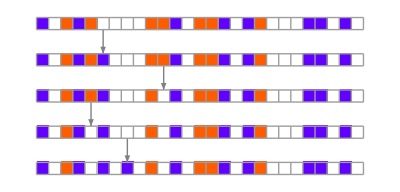

```mathematica
rulesmutationplot[diff[[-1, 1;;5]]]
```

```mathematica
ru = diff[[-1, 1]]; ru2 = diff[[-1, 2]];
```

```mathematica
getneutral[longrule]
```

{{5599982465655,3,1}}

```mathematica
g = NestGraph[getneutral, {longrule}, 2];
```

```mathematica
g
```

-Graphics-

```mathematica
verts = VertexList@g;
```

```mathematica
grouped = GroupBy[verts, getca];
```

```mathematica
gathered = GatherBy[verts, getca];
```

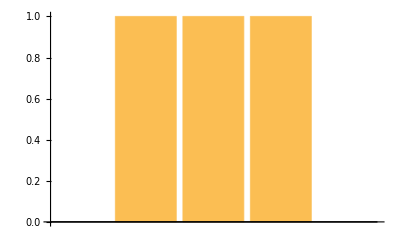

```mathematica
BarChart[Length/@gathered]
```

```mathematica
unique = DeleteDuplicatesBy[verts, getca];
```

```mathematica
Length@unique
```

3

-Graphics-

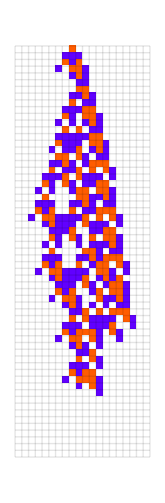

```mathematica
idx =1;
HighlightGraph[g, gathered[[idx]]]
plot@unique[[idx]]
```

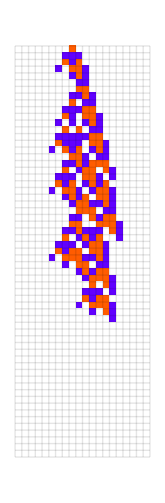
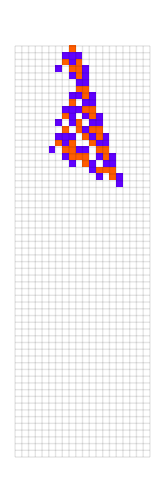
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@ unique
```

```mathematica
g2 = NestGraph[getneutral, {unique[[9]]}, 5]
```

-Graphics-

```mathematica
hg = HighlightGraph[g2, gathered2[[4]]]
```

-Graphics-

```mathematica
verts2= VertexList@g2;
gathered2 = GatherBy[verts2, getca];
unique2 = DeleteDuplicatesBy[verts2, getca];
```

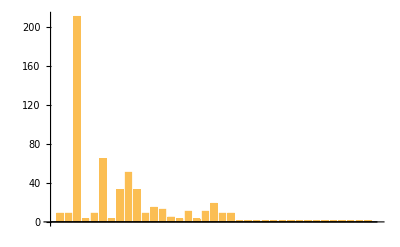

```mathematica
BarChart[Length/@ gathered2]
```

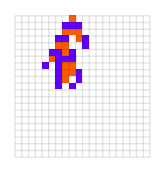
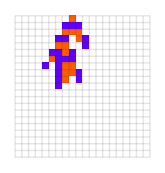
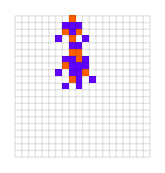
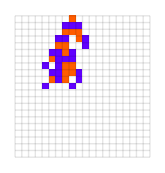
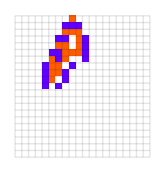
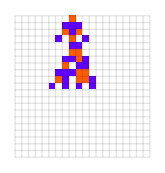
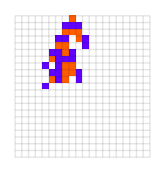
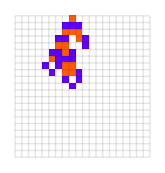

```mathematica
plot/@ unique2
```

### Random

```mathematica
diff = Nest[getmostdiff, {trirule}, 10];
```

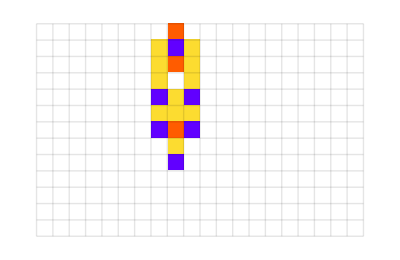
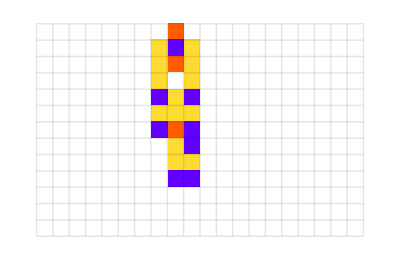
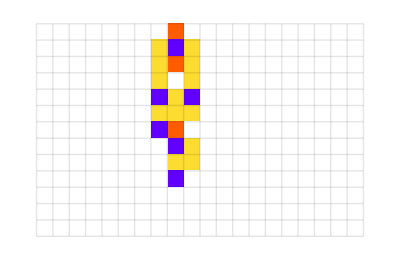
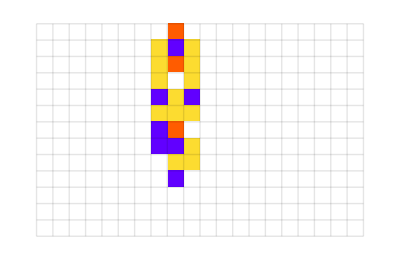
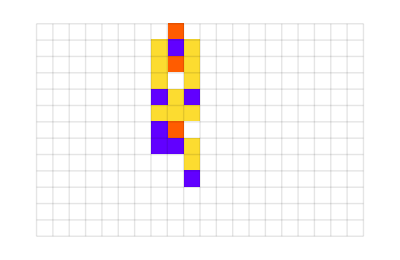
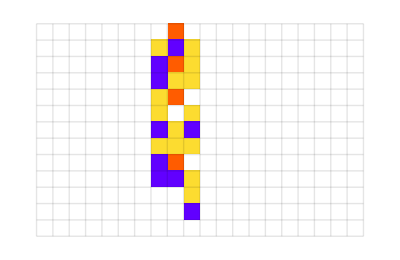
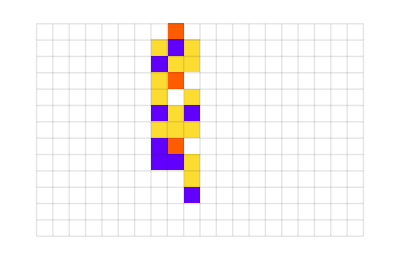
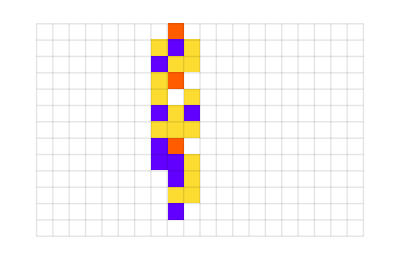
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@ diff
```

### Longer starting rules

```mathematica
testlifetime@longrule
```

52

```mathematica
plot@longrule
```

-Graphics-

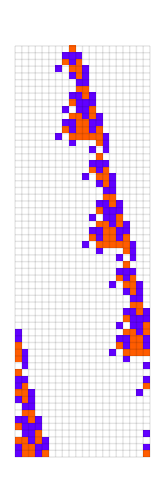
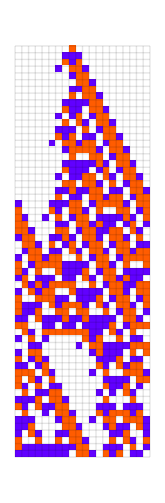
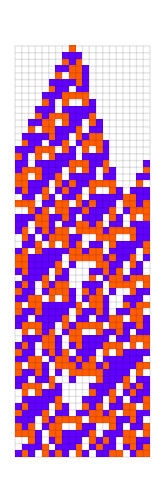
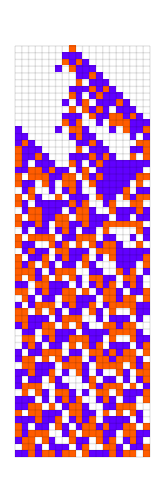
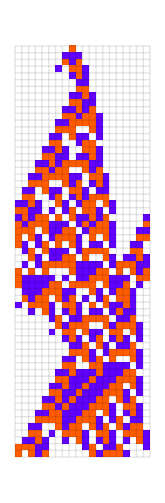
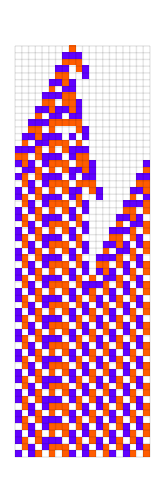
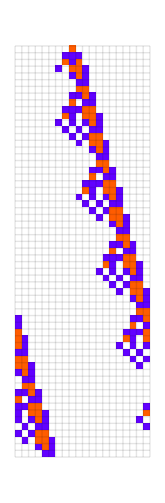
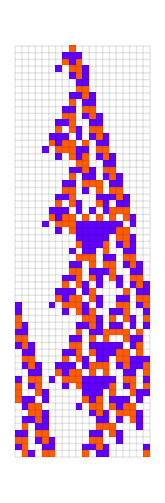
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@Table[randomrulemutation[longrule], 20]
```

### Exploring Fitness Neutral k = 2 r = 3/2

```mathematica
sgs = Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]];
sgs=Subgraph[mg,#]&/@sublevels
];
```

```mathematica
mg =  Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2]
];
```

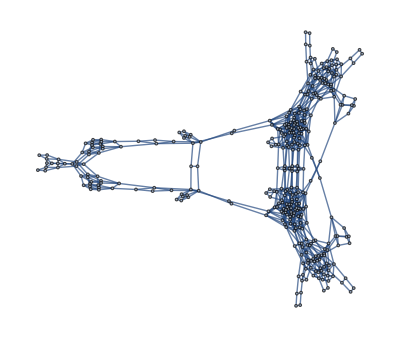

```mathematica
sgs[{4, 1}]
```

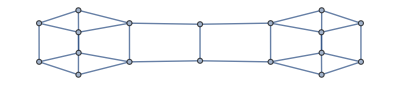

```mathematica
sgs[{3, 5}]
```

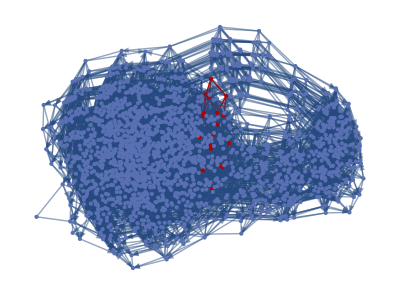

```mathematica
HighlightGraph[mg, sgs[{3, 4}]]
```

```mathematica
sls =  Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]]
];
```

```mathematica
meanatidx[{i_, j_}, cas_] := Mean[#[[i, j]] & /@ cas]
```

```mathematica
getmean[cas_] := Map[meanatidx[#, cas] &, Table[{i, j}, {i, 1, Length@cas[[1]]}, {j, 1, Length@cas[[1, 1]]} ], {2}]
```

```mathematica
getca232[ruleidx_] := CellularAutomaton[{ruleidx, 2, 3/2},
  {{1, 1, 1, 0, 1, 1, 1}, 0}, 8]
```

```mathematica
Keys[sgs]
```

{{1,1},{2,1},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{10,1},{10,2}}

```mathematica
idx = {3, 2};
verts = VertexList@sgs[idx];
uniquerules = DeleteDuplicatesBy[verts, getca232];
gathered = ReverseSortBy[GatherBy[verts, getca232], Length];
uniquecas =  getca232/@ gathered[[All, 1]];
uniquephenos = {{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{150,Automatic}]&/@ uniquecas;
cas = getca232/@ Flatten[gathered] ;
allphenos =  {{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{150,Automatic}]&/@ cas;
(*phenomean = getmean[cas];*)
lengths = Length/@ gathered;
```

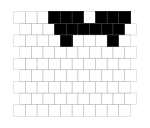
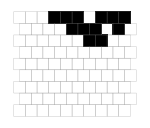
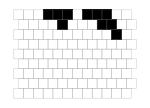
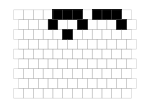
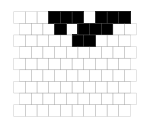
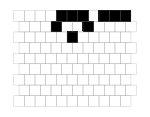
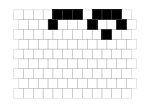
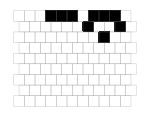

```mathematica
uniquephenos
```

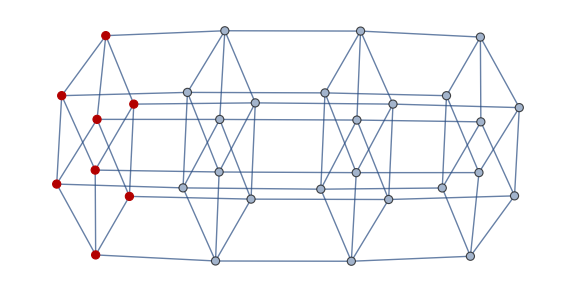
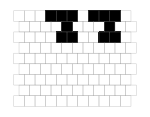
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
phenoidx = 3;
styled = MapAt[Style[#, Red]&, lengths, phenoidx];
{HighlightGraph[sgs[idx], gathered[[phenoidx]], ImageSize->Large], uniquephenos[[phenoidx]], BarChart[styled]}
```

### Exploring entire k=2 r = 3/2 entire mutation graph

```mathematica
mg
```

-Graphics-

```mathematica
vs = VertexList@mg;
```

```mathematica
cas = getca232/@ vs;
```

```mathematica
plotca[cas[[1500]]]
```

-Graphics-

```mathematica
idx = {4, 1};
verts = VertexList@mg;
```

```mathematica
Length@verts
```

1884

```mathematica
uniquerules = DeleteDuplicatesBy[verts, getca232];
```

```mathematica
gathered = ReverseSortBy[GatherBy[verts, getca232], Length];
uniquecas =  getca232/@ gathered[[All, 1]];
uniquephenos = {{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{150,Automatic}]&/@ uniquecas;
cas = getca232/@ Flatten[gathered] ;
allphenos =  {{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{150,Automatic}]&/@ cas;
phenomean = getmean[cas];
lengths = Length/@ gathered;
```

```mathematica
phenoidx = 3;
styled = MapAt[Style[#, Red]&, lengths, phenoidx];
{out = HighlightGraph[mg, Subgraph[mg, sgs[idx]], ImageSize->Large], uniquephenos[[phenoidx]], BarChart[styled]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph3D[out]
```

-Graphics3D-

```mathematica
Length@cas
```

1884

```mathematica
ArrayPlot[Rest[getmean[cas[[;;800]]]]]
```

-Graphics-

### Exploring k = 2, r = 1

```mathematica
VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}
```

```mathematica
RandomReal[{0, 1}, 10]
```

{0.55944,0.322562,0.119458,0.565757,0.164011,0.0467503,0.632217,0.592165,0.0411078,0.209142}

```mathematica
(*Generate weights based on the Pareto distribution*)
array=Range[10];            (*Example array:{1,2,...,10}*)
sampleSize=3;               (*Number of samples to take*)
paretoShape=4.0;
```

```mathematica
tups =Tuples[{1,0},7];
ug = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@tups],EdgeStyle->Opacity[.4,Gray], VertexSize->0];
```

```mathematica
weights=RandomVariate[NormalDistribution[10,1],Floor[Length[tups] / 20]];
```

```mathematica
weights = {0.05, 0.05, 0.8, 0.05, 0.05};
```

```mathematica
(*Normalize weights to form probabilities*)
(*ps=weights/Total[weights];*)
flat = Flatten[Table[#, 20]&/@ weights];
psdup = PadRight[flat, Length[tups], flat[[-1]]];
```

```mathematica
psdup
```

{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05}

```mathematica
BarChart[psdup]
```

-Graphics-

```mathematica
vs = VertexList[ug];
```

```mathematica
idx = 5;
{vs[[idx]], tups[[idx]]}
```

{{1,1,1,0,1,1,1},{1,1,1,1,0,1,1}}

```mathematica
ArrayPlot@bfsv
```

-Graphics-

```mathematica
degrees=VertexDegree[ug]
```

{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

```mathematica
sample=RandomSample[psdup->vs,Length[tups]/4];
HighlightGraph[ug, sample,VertexSize->Large, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

```mathematica
ng = NeighborhoodGraph[ug, vs[[1]], 3];
HighlightGraph[ug, ng]
```

```mathematica
ngv =VertexList@ng;
rand = RandomSample[ngv, 30];
Subgraph[ug, rand]
```

-Graphics-

```mathematica
Table[
ug = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},j]],EdgeStyle->Opacity[.4,Gray],VertexSize->0];
tups =Tuples[{1,0},j];
rand = RandomSample[tups, Floor[Length[tups]/4]];
Subgraph[ug, rand], {j, 3, 10}]
(*hg = HighlightGraph[ug, Subgraph[ug, rand]]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomVariate[ParetoDistribution[0.1, 1], 10]
```

{0.436867,0.247091,0.157765,5.76071,2.22024,0.105251,0.24756,0.200414,0.211725,0.358749}

```mathematica
Table[
ug = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},j]],EdgeStyle->Opacity[.4,Gray],VertexSize->0];
tups =Tuples[{1,0},j];
rand = Downsample[tups, 10];
Subgraph[ug, rand], {j, 3, 10}]
(*hg = HighlightGraph[ug, Subgraph[ug, rand]]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph3D[hg, EdgeStyle->Opacity[0.1]]
```

```mathematica
ugplain = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},9]],EdgeStyle->Opacity[.4,Gray],VertexSize->0];

vs = VertexList[ugplain];
vfit=Select[vs,SequencePosition[#,{{1, 0, 0, 1}}]!={}&];
```

```mathematica
tups = Flatten[Tuples[{1,0},#]&/@ Range[1, 9], 1];
```

```mathematica
tups = Tuples[{1,0},6];
```

```mathematica
Length@tups
```

64

```mathematica
FirstPosition[tups, {1, 0, 0, 1}]
```

{21}

```mathematica
allgs = Table[
ugplain =  UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},7]],EdgeStyle->Opacity[.4,Gray],VertexSize->0];
vs = VertexList[ugplain];
vfit=Select[vs,SequencePosition[#,tups[[i]]]!={}&];
ccs = ConnectedComponents[Subgraph[ugplain, vfit]];
sgs = Map[Subgraph[ugplain,#]&,ccs], {i, Length@tups}];
```

```mathematica
positions =Position[allgs, _List?(Length[#]>1&)];
```

```mathematica
positions
```

{{21},{24},{33},{35},{36},{37},{39},{40},{41},{42},{43},{44},{45},{48},{49},{50},{51},{52},{53},{54},{56},{57},{58},{60},{65},{67},{68},{69},{71},{72},{73},{74},{75},{76},{77},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{109},{110},{112},{113},{114},{115},{116},{117},{118},{120},{121},{122},{124},{}}

```mathematica
allgs[[;;10]]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
tups[[#]]&/@ positions;
```

```mathematica
ArrayPlot/@(tups[[#]]&/@ positions)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allgs[[#]]&/@ positions[[;;10]]
```

{{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}}}

```mathematica
tups[[positions[[3]]]]
allgs[[positions[[3]]]]
```

{{1,0,1,1,0}}

{{-Graphics-,-Graphics-}}

```mathematica
hg = HighlightGraph[ugplain, allgs[[15]], GraphHighlightStyle->"Thick"]
```

```mathematica
ccs = ConnectedComponents[Subgraph[ugplain, vfit]];
```

```mathematica
ccs[[2]]
```

{{1,1,1,1,0,1,0,1,1},{1,1,1,1,0,1,0,1,0},{0,1,1,1,0,1,0,1,1},{1,0,1,1,0,1,0,1,1},{1,1,0,1,0,1,0,1,1},{0,1,1,1,0,1,0,1,0},{1,0,1,1,0,1,0,1,0},{1,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,1},{0,0,1,1,0,1,0,1,1},{1,0,0,1,0,1,0,1,1},{1,1,0,1,0,1,1,1,1},{1,1,0,1,0,1,0,0,1},{0,1,0,1,0,1,0,1,0},{0,0,1,1,0,1,0,1,0},{1,0,0,1,0,1,0,1,0},{1,1,0,1,0,1,1,1,0},{1,1,0,1,0,1,0,0,0},{0,1,0,1,0,1,1,1,1},{0,1,0,1,0,1,0,0,1},{0,0,0,1,0,1,0,1,1},{1,1,0,1,0,1,1,0,1},{0,1,0,1,0,1,1,1,0},{0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0},{1,1,0,1,0,1,1,0,0},{0,1,0,1,0,1,1,0,1},{0,1,0,1,0,1,1,0,0}}

```mathematica
ug = Graph[ugplain, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}];
```

```mathematica
hg = HighlightGraph[ugplain,allgs[[15]]]
```

```mathematica
Graph3D[hg, EdgeStyle->Opacity[0]]
```

-Graphics3D-

```mathematica
Graph3D[Subgraph[ugplain, vfit]]
```

-Graphics3D-

```mathematica
GridGraph[{3,5},VertexSize->{2->Medium},GraphHighlightStyle->"Thick"];
Reap[DepthFirstScan[%,2,{"FrontierEdge"->Sow}]][[2,1]]//HighlightGraph[%,#]&
```

```mathematica
bfs = Reap[BreadthFirstScan[Subgraph[ug, vfit], 
  vfit[[1]],{"FrontierEdge"->Sow}]][[2, 1]];
```

```mathematica
bfsv = Reap[BreadthFirstScan[Subgraph[ug, vfit], 
  vfit[[1]],{"DiscoverVertex"->(Sow[#1]&)}]][[2, 1]];
```

```mathematica
bfsg = Graph[bfs, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

```mathematica
HighlightGraph[Subgraph[ug, vfit], bfsv, VertexLabels->None, VertexSize->Automatic]
```

-Graphics-

```mathematica
getmutes[arr_]:=Table[
gene = arr[[i]];
mutedigits = DeleteCases[Range[0, 2- 1], gene];
mutes = ReplacePart[arr, i -> flip[arr[[i]]]],
{i,Length[arr]}]
```

```mathematica
ng = NestGraph[getmutes, {vs[[1]]}, 7]
ngvs = VertexList[ng];
ArrayPlot[ngvs]
```

-Graphics-

-Graphics-

```mathematica
Subgraph[ug, vfit]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[#,CenterArray[{1,1,1,0,1,1,1},7+10],5],Mesh->True,ImageSize->100]&/@ Range[0, 128];
```

### Showing broad principle based on k = 2 r = 1

```mathematica
tupslist = Table[Tuples[{1,0},i], {i, 1, 12}];
```

```mathematica
ugs = Table[UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@tupslist[[j]]],EdgeStyle->Opacity[.4,Gray],VertexSize->0], {j, 1, Length[tupslist]}];
```

```mathematica
ugs[[4]] // VertexList // Length
```

16

```mathematica
samples = Table[RandomSample[#, Floor[(Length[#]/10)*i]], {i, 1, 10}]&/@ tupslist;
```

```mathematica
getsgs[g_, samples_]:= Subgraph[g, #]&/@samples;
```

```mathematica
sgslist = MapThread[getsgs, {ugs, samples}];
```

```mathematica
sgslist[[7]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
edgeslist = Map[EdgeCount[#]&, sgslist[[4;;]], {2}];
```

```mathematica
ListPlot3D[edgeslist]
```

-Graphics3D-

```mathematica
Table[
ug = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},j]],EdgeStyle->Opacity[.4,Gray],VertexSize->0];
tups =Tuples[{1,0},j];
rand = RandomSample[tups, 200];
Subgraph[ug, rand], {j, 8, 10}]
```

```mathematica
ng = NeighborhoodGraph[ug, vs[[1]], 3];
HighlightGraph[ug, ng]
```

```mathematica
ngv =VertexList@ng;
rand = RandomSample[ngv, 30];
Subgraph[ug, rand]
```

### Running get neutral on genotype space

### Exploring k = 3, r = 1 rules now

```mathematica
nr = gathered[[5, 1]]
```

{474448786161,3,1}

```mathematica
plot@nr
```

-Graphics-

```mathematica
g = NestGraph[getneutral, {nr}, 5];
```

```mathematica
verts = VertexList@g;
```

```mathematica
uniquerules = DeleteDuplicatesBy[verts, getca];
```

```mathematica
gathered = ReverseSortBy[GatherBy[verts, getca], Length];
uniquecas =  getca/@ gathered[[All, 1]];
uniqueplots = plot/@ gathered[[All, 1]];
```

```mathematica
uniqueplots
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cas = getca/@ Flatten[gathered, 1] ;
phenomean = getmean[cas];
lengths = Length/@ gathered;
```

```mathematica
ArrayPlot[Rest[getmean[cas]]]
```

-Graphics-

```mathematica
phenoidx = 5;
styled = MapAt[Style[#, Red]&, lengths, phenoidx];
{HighlightGraph[g, Subgraph[g, gathered[[phenoidx]]]], uniqueplots[[phenoidx]], BarChart[styled]}
```

{-Graphics-,-Graphics-,-Graphics-}

### Creating pure phenotype graphs

Get graph 5 steps deep

```mathematica
g = NestGraph[getneutral, {initrule}, 5];
```

```mathematica
verts = VertexList@g;
uniquerules = DeleteDuplicatesBy[verts, getca];
gathered = ReverseSortBy[GatherBy[verts, getca], Length];
uniquecas =  getca/@ gathered[[All, 1]];
uniqueplots = plot/@ gathered[[All, 1]];
```

```mathematica
pairs = Subsets[uniquerules, {2}];
capairs = Map[getca, pairs, {2}];
edges = #1<->#2&@@@pairs;
diffs = getdiff@@@capairs;
mostdiff = TakeLargestBy[uniquerules,getdiffrule[initrule, #]&, 1][[1]];
```

```mathematica
initrule
```

{5586032021307,3,1}

```mathematica
g=Graph[edges,EdgeWeight->diffs, GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexShapeFunction->(Inset[plot[#2, ImageSize->Tiny], #1]&)]
```

-Graphics-

### Building on pure phenotype graph

```mathematica
g = NestGraph[getneutral, {mostdiff}, 5];
```

```mathematica
verts = VertexList@g;
uniquerules = DeleteDuplicatesBy[verts, getca];
gathered = ReverseSortBy[GatherBy[verts, getca], Length];
uniquecas =  getca/@ gathered[[All, 1]];
uniqueplots = plot/@ gathered[[All, 1]];
```

```mathematica
pairs = Subsets[uniquerules, {2}];
capairs = Map[getca, pairs, {2}];
edges = #1<->#2&@@@pairs;
diffs = getdiff@@@capairs;
mostdiff = TakeLargestBy[uniquerules,getdiffrule[initrule, #]&, 1][[1]];
```

```mathematica
g=Graph[edges,EdgeWeight->diffs, GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexShapeFunction->(Inset[plot[#2, ImageSize->{50, Automatic}], #1]&)]
```

-Graphics-

```mathematica
g = NestGraph[getneutral, {mostdiff}, 5];
```

```mathematica
verts = VertexList@g;
uniquerules = DeleteDuplicatesBy[verts, getca];
gathered = ReverseSortBy[GatherBy[verts, getca], Length];
uniquecas =  getca/@ gathered[[All, 1]];
uniqueplots = plot/@ gathered[[All, 1]];
```

```mathematica
pairs = Subsets[uniquerules, {2}];
capairs = Map[getca, pairs, {2}];
edges = #1<->#2&@@@pairs;
diffs = getdiff@@@capairs;
mostdiff = TakeLargestBy[uniquerules,getdiffrule[initrule, #]&, 1][[1]];
```

```mathematica
ReverseSort[diffs][[;;10]]
```

{55,55,55,54,54,54,53,53,53,53}

```mathematica
plot@mostdiff
```

-Graphics-

```mathematica
g=Graph[edges,EdgeWeight->diffs, GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexShapeFunction->(Inset[plot[#2, ImageSize->{50, Automatic}], #1]&)]
```

-Graphics-

```mathematica
ClearAll@phenospacegraph
```

```mathematica
phenospacegraph[rule_, steps_:5]:= Module[{},
ng = NestGraph[getneutral, {rule}, steps];
verts = VertexList@ng;
uniquerules = DeleteDuplicatesBy[verts, getca];
gathered = ReverseSortBy[GatherBy[verts, getca], Length];
uniquecas =  getca/@ gathered[[All, 1]];
uniqueplots = plot/@ gathered[[All, 1]];
pairs = Subsets[uniquerules, {2}];
capairs = Map[getca, pairs, {2}];
edges = #1<->#2&@@@pairs;
diffs = getdiff@@@capairs;
mostdiff = TakeLargestBy[uniquerules,getdiffrule[initrule, #]&, 1][[1]];
Sow[mostdiff];
psg=Graph[edges,EdgeWeight->diffs,EdgeShapeFunction->Automatic, EdgeLabels->"EdgeWeight", GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexShapeFunction->Automatic]
]
```

```mathematica
(Inset[plot[#2, ImageSize->{50, Automatic}], #1]&)
```

```mathematica
psg1 = phenospacegraph[initrule, 5]
```

{1,10,11,10,2,27,20,38,10,12,11,1,28,19,38,14,13,11,23,19,34,1,13,28,16,34,12,29,17,35,28,18,39,26,40,38}

{4738870962078,3,1}

-Graphics-

```mathematica
v1s = VertexList@psg1;
```

```mathematica
{4738870962078,3,1}
```

```mathematica
psg2 = phenospacegraph[ {4738870962078,3, 1}, 5]
```

{4551746925183,3,1}

-Graphics-

```mathematica
HighlightGraph[psg2,v1s]
```

-Graphics-

```mathematica
plot@{4551746925183,3,1}
```

-Graphics-

```mathematica
combinephenographs[graph1_, graph2_]:= Module[{},
v1 = VertexList@graph1;
v2 = Complement[VertexList@graph2, v1];
verts = Union[v1, v2];
pairs = Subsets[verts, {2}];
(*plots = Map[plot, pairs, {2}];
Echo@plots;*)
capairs = Map[getca, pairs, {2}];
edges = #1<->#2&@@@pairs;
diffs = getdiff@@@capairs;
Graph[edges[[;;100]],EdgeWeight->diffs[[;;100]],EdgeLabels->"EdgeWeight", GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexShapeFunction->Automatic, VertexSize->0.01]
]
```

```mathematica
(vsf[#1, #2, v1, v2]&)
```

```mathematica
vsf[loc_, vert_, v1_, v2_]:=
If[MemberQ[v1, vert],
Inset[plot[vert, ImageSize->{50, Automatic}], loc],
Inset[plot[vert, ImageSize->{50, Automatic}, ColorRules->Join[{0->LightRed}, customstyledata["Colors"][[2;;]]]], loc]]
```

```mathematica
psg1
```

-Graphics-

```mathematica
vsf[{1, 1}, VertexList[psg1][[1]], v1, v2]
```

Inset[-Graphics-,{1,1}]

```mathematica
psg2
```

-Graphics-

```mathematica
{#, plot[#]}&/@ v2
```

```mathematica
getdiffrule[{4738870962078,3, 1}, {4738713183393,3,1}]
```

27

```mathematica
getdiffsfromgraph[]
```

```mathematica
cg = combinephenographs[psg1, psg2]
```

-Graphics-

```mathematica
{plot@v1s[[7]], plot@v2[[7]]}
```

{-Graphics-,-Graphics-}

```mathematica
getdiffrule[v1s[[7]], v2[[7]]]
```

44

```mathematica
pairs[[;;10]]
```

{{{2203935301530,3,1},{2203935301536,3,1}},{{2203935301530,3,1},{4550559154548,3,1}},{{2203935301530,3,1},{4550584718391,3,1}},{{2203935301530,3,1},{4550584722765,3,1}},{{2203935301530,3,1},{4550587847988,3,1}},{{2203935301530,3,1},{4550587852362,3,1}},{{2203935301530,3,1},{4551718227369,3,1}},{{2203935301530,3,1},{4551746920809,3,1}},{{2203935301530,3,1},{4551746925183,3,1}},{{2203935301530,3,1},{4551751708152,3,1}}}

```mathematica
{v1s[[7]], v2[[7]]}
```

{{5565120882945,3,1},{4550587852362,3,1}}

```mathematica
FirstPosition[pairs, {v2[[7]], v1s[[7]]}]
```

{276}

```mathematica
diffs[[276]]
```

44

```mathematica
edges[[276]]
```

{4550587852362,3,1}<->{5565120882945,3,1}

```mathematica
Subgraph[cg, {edges[[276]]}, EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
pairs[[1, 1]]
```

{2203935301530,3,1}

```mathematica
pairs[[50, 1]]
```

{2203935301536,3,1}

```mathematica
FirstPosition[pairs,{pairs[[1, 1]], pairs[[50, 1]]}]
```

{1}

```mathematica
diffs[[1]]
```

40

```mathematica
HighlightGraph[cg, pairs[[1, 1]], GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
BarChart[diffs[[;;200]]]
```

-Graphics-

```mathematica
Length@VertexList@psg2
```

37

```mathematica
Length@VertexList@cg
```

45

```mathematica
psg2 = phenospacegraph[ {4738870962078,3, 1}, 5]
```

```mathematica
customstyledata["Colors"][[2;;]]
```

{1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]}

```mathematica
plot[{4551746925183,3,1}]
```

-Graphics-

```mathematica
g=Graph[{1<->2,2<->3,3<->1},EdgeWeight->{5,7,3},VertexLabels->"Name",EdgeLabels->"EdgeWeight"]
```

-Graphics-

### Feature Space Plot

```mathematica
getuniquephenos[initrule_, steps_:5]:=Module[{},
ng = NestGraph[getneutral, {initrule}, steps];
verts = VertexList@ng;
uniquerules = DeleteDuplicatesBy[verts, getca]
]
(*getdiffs[rules_]:=Module[{},
pairs = Subsets[rules, {2}];
capairs = Map[getca, pairs, {2}];
diffs = getdiff@@@capairs
]*)
getmostdiff[initrule_, rules_]:=TakeLargestBy[rules,getdiffrule[initrule, #]&, 1][[1]];
```

```mathematica
uniquephenos1 = getuniquephenos[initrule];
```

```mathematica
uniqueplots = plot/@ uniquephenos1;
```

```mathematica
fsp = FeatureSpacePlot[uniqueplots];
```

```mathematica
coords = Cases[fsp[[1]], Point[_], Infinity][[1, 1]];
```

```mathematica
coords[[7]]
```

{-8.01474,-6.16174}

```mathematica
ListPlot[coords]
```

-Graphics-

```mathematica
Position[uniquephenos1, initrule]
```

{{1}}

```mathematica
fsp
```

-Graphics-

```mathematica
md = uniquephenos1[[7]]
```

{5565120882945,3,1}

```mathematica
md2 = getmostdiff[initrule, uniquephenos1]
```

{4738870962078,3,1}

```mathematica
up2 = getuniquephenos[md];
```

```mathematica
up2white = plot/@ up2;
```

```mathematica
Length@up2
```

89

```mathematica
uplots2 = plot[#, ColorRules->Join[{0->LightRed}, {1->Red, 2->Blue}]]&/@ up2;
```

```mathematica
uplots2[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot[{4738870962078,3,1}]
```

-Graphics-

```mathematica
fsp2 = FeatureSpacePlot[uplots2]
```

-Graphics-

```mathematica
fsp3 = FeatureSpacePlot@Join[uniqueplots, uplots2]
```

-Graphics-

Questions I want to answer:
How much does the individual mutation matter?
Okay let me think. So basically

### Phenograph where distance is connectivity

```mathematica
getuniquephenos[rule_]:=Module[{},
n = getneutral[rule];
Echo@Length@n;
DeleteDuplicatesBy[n, getca]
]
```

```mathematica
getuniquephenos[initrule]
```

9

{{5554650961698,3,1},{5585902881144,3,1}}

```mathematica
plot/@{{5554650961698,3,1},{5585902881144,3,1}}
```

{-Graphics-,-Graphics-}

```mathematica
getuniquephenos/@ %
```

```mathematica
Map[plot, {{{5586032021307,3,1},{5554521821535,3,1}},{{5554521821535,3,1},{5586032021307,3,1}}}, {2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[getuniquephenos, %, {2}]
```

{{{{5554650961698,3,1},{5585902881144,3,1}},{{5585902881144,3,1},{5554650961698,3,1}}},{{{5585902881144,3,1},{5554650961698,3,1}},{{5554650961698,3,1},{5585902881144,3,1}}}}

```mathematica
Map[getuniquephenos, %, {3}]
```

{{{{{5586032021307,3,1},{5554521821535,3,1}},{{5554521821535,3,1},{5586032021307,3,1}}},{{{5554521821535,3,1},{5586032021307,3,1}},{{5586032021307,3,1},{5554521821535,3,1}}}},{{{{5554521821535,3,1},{5586032021307,3,1}},{{5586032021307,3,1},{5554521821535,3,1}}},{{{5586032021307,3,1},{5554521821535,3,1}},{{5554521821535,3,1},{5586032021307,3,1}}}}}

```mathematica
(Inset[plot[#2, ImageSize->{50, Automatic}], #1]&)
```

```mathematica
g = NestGraph[getneutral, {initrule}, 3, VertexShapeFunction->Automatic]
```

-Graphics-

```mathematica
vp = DeleteDuplicatesBy[VertexList@g, getca];
```

```mathematica
Subgraph[g, vp]
```

-Graphics-

```mathematica
getunique[rule_, searchdepth_:3]:=Module[{},
g = NestGraph[getneutral, {rule}, searchdepth, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
vp = DeleteCases[DeleteDuplicatesBy[VertexList@g, getca], rule]
]
```

```mathematica
ng = NestGraph[getunique, {initrule}, 4, VertexShapeFunction->(Inset[plot[#2, ImageSize->{50, Automatic}], #1]&)]
```

-Graphics-

```mathematica
Graph[ng, GraphLayout->"LayeredDigraphEmbedding", VertexShapeFunction->(Inset[plot[#2, ImageSize->{20, Automatic}], #1]&), AspectRatio->1/2]
```

-Graphics-

```mathematica
DuplicateFreeQ[VertexList@ng]
```

True

```mathematica
sg = Subgraph[ng, uqv, VertexCoordinates->coords, VertexShapeFunction->Automatic]
```

-Graphics-

```mathematica
edgefunc[edge]
```

```mathematica
sgEdges = EdgeList[sg];
```

```mathematica
sgEdges[[1]]
```

{5554650961698,3,1}->{5586032021307,3,1}

```mathematica
Cases[sgEdges, uqv[[1]]->_]
```

{{5586032021307,3,1}->{5554650961698,3,1},{5586032021307,3,1}->{5585888536611,3,1},{5586032021307,3,1}->{5586146816937,3,1},{5586032021307,3,1}->{7280738380356,3,1}}

```mathematica
idx = 8;
```

```mathematica
idx
```

28

```mathematica
uqv[[idx]]
```

{3023299693473,3,1}

```mathematica
Cases[sgEdges, uqv[[50]]->_]
```

{}

```mathematica
sgEdges[[;;10]]
```

{{5554650961698,3,1}->{5586032021307,3,1},{5586032021307,3,1}->{5554650961698,3,1},{5586032021307,3,1}->{5585888536611,3,1},{5586146816937,3,1}->{5585888536611,3,1},{5586032021307,3,1}->{5586146816937,3,1},{5585888536611,3,1}->{5586146816937,3,1},{7280738380356,3,1}->{5586146816937,3,1},{5586032021307,3,1}->{7280738380356,3,1},{5554650961698,3,1}->{5554660529742,3,1},{5585888536611,3,1}->{5586146875905,3,1}}

```mathematica
Cases[sgEdges, _->uqv[[idx]] || uqv[[idx]]->_]
```

{{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_,{4551718227369,3,1}||{4551718227369,3,1}→_}

```mathematica
idx = 1
```

1

```mathematica
uqv[[idx]]
```

{4550587847988,3,1}

```mathematica
Join[Cases[sgEdges, uqv[[idx]]->_ ], Cases[sgEdges, _->uqv[[idx]]]]
```

{{4738871021370,3,1}->{4551746920809,3,1}}

```mathematica
{HighlightGraph[sg, Cases[sgEdges, uqv[[idx]]->_ ], ImageSize->Large, VertexShapeFunction->], plot[uqv[[idx]]]}
idx +=1;
```

{-Graphics-,-Graphics-}

```mathematica
idx = 22
```

22

```mathematica
plot@uqv[[22]]
```

-Graphics-

```mathematica
NeighborhoodGraph[]
```

```mathematica
{HighlightGraph[sg, NeighborhoodGraph[sg, uqv[[idx]]]], plot[uqv[[idx]]]}
idx +=1;
```

{-Graphics-,-Graphics-}

```mathematica
uqv = DeleteDuplicatesBy[VertexList@ng, getca];
```

```mathematica
Length@VertexList@g
```

193

```mathematica
Length@uqv
```

107

```mathematica
ngplots = plot/@ uqv;
```

```mathematica
ngplots[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fsp4[[1, 3, 2, 2, 1, 1, All, 1]]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
fsp4 = FeatureSpacePlot[ngplots]
```

-Graphics-

```mathematica
coords = Cases[fsp4[[1]], Point[_], Infinity][[1, 1]];
```

```mathematica
plots = Cases[fsp4[[1]], Text[_], Infinity];
```

```mathematica
plots
```

{}

### Gathering mutations instead of deleting

```mathematica
g = NestGraph[getneutral, {initrule}, 11, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
```

```mathematica
vs = VertexList@g;
```

```mathematica
Length@vs
```

4975

```mathematica
getcaedge[start_->dest_]:= getca[start]->getca[dest]
```

```mathematica
phenograph[graph_]:=Module[{},
es = EdgeList@g;
caedges = getcaedge/@ EdgeList[g];
phenoedges = DeleteCases[DeleteDuplicates[caedges],x_->x_];
Graph[phenoedges]
]
```

```mathematica
gatheredges[graph_]:= Module[{}, 
es = EdgeList@g;
GatherBy[es, getcaedge];
caedges = getcaedge/@ EdgeList[g];
]
```

```mathematica
pg = phenograph[g]
```

-Graphics-

```mathematica
Graph[pg, EdgeStyle->{initrule->Red}]
```

-Graphics-

```mathematica
es = EdgeList[pg];
```

```mathematica
es[[1]]
```

{5586032021307,3,1}->{5554650961698,3,1}

```mathematica
Cases[es, vs[[1]]->_ ];
```

```mathematica
ArrayPlot[vs[[idx - 1]], ColorRules->{0->White, 1->Red, 2->Blue}]
```

-Graphics-

```mathematica
idx = -75;
```

```mathematica
idx
```

85

```mathematica
{fspgraph = Graph[pg, VertexShapeFunction->Automatic, VertexCoordinates->coords, EdgeStyle->{_->_->Transparent,vssorted[[idx]]->_->Orange} , ImageSize->{750, Automatic}],
ArrayPlot[vssorted[[idx]], ColorRules->{0->White, 1->Red, 2->Blue}]}
Length[Cases[es,vssorted[[idx]]->_ ]]
idx -= 1
```

{-Graphics-,-Graphics-}

0

-83

```mathematica
vssorted = ReverseSortBy[vs, Length[Cases[es,#->_ ]]&];
```

```mathematica
vs = VertexList@pg;
idx = 1;
```

```mathematica
Cases[es, vs[[idx]]->_ ]
```

{}

```mathematica
HighlightGraph[fspgraph, Cases[es, vs[[idx]]->_ ]]
idx += 1;
```

-Graphics-

```mathematica
plots = ArrayPlot[#, ImageSize->{60, Automatic}, ColorRules->{0->White, 1->Red, 2->Blue}]&/@ vs;
```

```mathematica
plots[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fsp5 = FeatureSpacePlot[plots];
```

```mathematica
fsp5
```

-Graphics-

```mathematica
coords = Cases[fsp5[[1]], Point[_], Infinity][[1, 1]];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/coords1.csv", coords]
```

Projects/Wolfram/CAEvolution/coords1.csv

```mathematica
gathered = GatherBy[vs, getca];
```

```mathematica
gathersorted = ReverseSortBy[gathered, Length];
```

```mathematica
Length@gathered
```

222

```mathematica
BarChart[Length/@ gathersorted]
```

-Graphics-

```mathematica
plot/@ gathered[[150;;, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gatherunique[rules_, depth_:3]:=Module[{},
g = NestGraph[getneutral, rules, depth, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
gathered = ReverseSortBy[GatherBy[VertexList@g, getca], Length];
]
```

```mathematica
ng = NestGraph[getunique, {initrule}, 4, VertexShapeFunction->(Inset[plot[#2, ImageSize->{50, Automatic}], #1]&)]
```

### Trying to get all k =3 r = 1 rules

```mathematica
Text@Grid[Prepend[Catenate@Table[
Flatten[{k,r,Row[{With[{kk=k},HoldForm[kk^#]],If[k^#>10^6,"≈" ,"="],If[k^#>10^6,N[k^#,4],k^#]}]&/@{k^(2r+1)-1,Length[Union[First[Sort[{#,Reverse[#]}]]&/@Tuples[Range[k],2r+1]]]-1}}],{k,2,4},{r,1,2,1/2}],{Style["k",Italic],Style["r",Italic],"general","symmetric"}],Frame->All,FrameStyle->GrayLevel[0,.2],Spacings->{1, .6},Background->{White,{GrayLevel[.85]}}]
```

k | r | general | symmetric
2 | 1 | 2^7=128 | 2^5=32
2 | 3/2 | 2^15=32768 | 2^9=512
2 | 2 | 2^31≈2.147×10^9 | 2^19=524288
3 | 1 | 3^26≈2.542×10^12 | 3^17≈1.291×10^8
3 | 3/2 | 3^80≈1.478×10^38 | 3^44≈9.848×10^20
3 | 2 | 3^242≈2.906×10^115 | 3^134≈8.595×10^63
4 | 1 | 4^63≈8.507×10^37 | 4^39≈3.022×10^23
4 | 3/2 | 4^255≈3.352×10^153 | 4^135≈1.897×10^81
4 | 2 | 4^1023≈8.079×10^615 | 4^543≈8.29×10^326

```mathematica
ListLogLogPlot[Counts[Values[]+1],Frame->True,AspectRatio->1/2,FrameLabel->{"lifetime"}]
```

-Graphics-

```mathematica
ListLogLogPlot[Counts[Values[samp]+1],Frame->True,AspectRatio->1/2,FrameLabel->{"lifetime"}]
```

-Graphics-

```mathematica
ruledict = ;
```

```mathematica
samp = RandomSample[ruledict, 5000];
```

```mathematica
allmutes = getallmutations[{#, 3, 1}]&/@ Keys[samp];
```

```mathematica
allmuten = Select[#, (KeyExistsQ[samp, #[[1]]]&)]&/@ allmutes;
```

```mathematica
alledges = Flatten[MapThread[getedges, {Keys[samp], allmuten}], 1];
```

```mathematica
neutrals = Select[samp, # == 11&];
```

```mathematica
Length[neutrals]
```

976

```mathematica
getedges[rule_, mutes_]:= rule<->#&/@ mutes
```

```mathematica
alledges = Flatten[MapThread[getedges, {newtrules, allmuten}], 1];
```

```mathematica
(Inset[plot[#2, ImageSize->{30, Automatic}], #1]&)
```

```mathematica
g = Graph[alledges]
```

-Graphics-

```mathematica
ccs = ConnectedComponents[g];
```

```mathematica
ccs[[1]]
```

{{5233726138794,3,1},2691860310465,5233769185515,5233683092073,{149994482136,3,1},{2691903357186,3,1},{5233683092073,3,1},{5233769185515,3,1},5233726138794,149994541185,2597760178359,2691903357186,{2691860310465,3,1},{2597674084917,3,1},{2597760237408,3,1},{2597760178359,3,1},2597760237435,2597674084917,2597760237408,{2597717190714,3,1},{2597760237435,3,1},2597717191443,2597717190714,{2597674144722,3,1},{2597717191443,3,1},2601160929123,2597674144722,{2601160927665,3,1},{2601160929123,3,1},5143026755994,2601247021107,2601160927665,{5143112849436,3,1},{59381192778,3,1},{5143026755994,3,1},{2601247021107,3,1},5143116038082,5143112849436,{5143116038082,3,1}}

```mathematica
plot/@ ccs[[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@ neutrals[[;;50]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
newts = getneutral[{#, 3, 1}]&/@ neutrals[[;;50]];
```

```mathematica
newts
```

{{},{},{},{},{},{{36139920045,3,1}},{},{},{},{},{},{},{{14055180216,3,1},{48923024226,3,1},{45431456856,3,1}},{},{},{},{},{},{},{},{{84953307822,3,1},{53577031182,3,1}},{},{},{},{},{},{},{{55894939818,3,1},{55894408458,3,1}},{},{},{},{},{},{},{},{},{{57057970299,3,1}},{},{},{},{},{{88440092223,3,1},{57063815583,3,1}},{},{},{},{},{},{},{},{{58190588520,3,1},{58176241800,3,1}}}

```mathematica
pos = Position[newts, _List?(# != {}&)]
```

{{6,1},{6},{13,1},{13,2},{13,3},{13},{21,1},{21,2},{21},{28,1},{28,2},{28},{37,1},{37},{42,1},{42,2},{42},{50,1},{50,2},{50},{}}

```mathematica
plot/@ Flatten[n2, 1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pos
```

```mathematica
pos
```

{}

```mathematica
n2[[1]]
```

{{36139920045,3,1}}

```mathematica
plot[n2[[3, 1]]]
```

-Graphics-

```mathematica
NestGraph[getneutral,n2[[3]], 5]
```

-Graphics-

### Random for community post

```mathematica
diffsmemo = Import["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv"]
```

{{{109636419052937157723438118980837975564, 4, 1},{106977963061367325977630504860277286412, 4, 1},{106977963060438870948166469654102943244, 4, 1},{106977963060438870948166469654102943372, 4, 1},{106977963060438870948166469653968725644, 4, 1},{106977963060438870948166469104212911756, 4, 1},{106977963061676810987451849379112035980, 4, 1},{106977963061676813348635090813934642828, 4, 1},{106894886311940256106578602872667121292, 4, 1},{106894886311940256106578602872683898508, 4, 1},{106894886311945091809857061389382723212, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{109636419052937157723438681930791396876, 4, 1},{109636419052937006607711230102144558604, 4, 1},{109553342303200449365654742160877037068, 4, 1},{109221035304254220397428790395806950924, 4, 1},{109221035304254220397428790395806955020, 4, 1},{109221035304254220397428790395823732236, 4, 1},{109221035304256638249068019654173144588, 4, 1},{109221035304256638249068019654156367372, 4, 1},{110217956301095325153745874949366625804, 4, 1},{110217956301095325153745874948292883980, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{109636419052937157723438118980838499852, 4, 1},{109636419052937006607710667152191661580, 4, 1},{109304112053990777639484715387121575436, 4, 1},{109304112053990777639484715387122624012, 4, 1},{109304112053990777639484715387122623500, 4, 1},{109304112053990777648708087423977399308, 4, 1},{109298919757132242821079556927648179212, 4, 1},{109298919757132242821079556927649227788, 4, 1},{109298919757132242821079556927666005004, 4, 1},{109298919757132245182262798362488611852, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{109636419052937157723438118980838499852, 4, 1},{109636419052937157723438118980033193484, 4, 1},{109636419052937157723438118981106935308, 4, 1},{109636419052937157723438118981106935052, 4, 1},{109636419052937157723438118981106926860, 4, 1},{109639015201366425137252384229271536908, 4, 1},{109639015201366425137252385328783164684, 4, 1},{109639015201366425137252385328770581772, 4, 1},{109639015201366425137254637128584267020, 4, 1},{109639015201366428679029499280818177292, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{},{},{},{},{},{},{},{},{},{}},{{109636419052937157723438118980837975564, 4, 1},{106977963061367325977630504860277286412, 4, 1},{106977963061367325977630504859471980044, 4, 1},{106976989505706350697450155391410251276, 4, 1},{106976989505706350697450155391410267660, 4, 1},{106976989505707559623269770020584973836, 4, 1},{277118172966176791354957073736469079564, 4, 1},{277118172966176791354957073736469075468, 4, 1},{277118172966176791354812958548393219596, 4, 1},{277118176769128592039501163038502835724, 4, 1},{277118176452215941982443812664327034380, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{109636419052937157723438118978690491916, 4, 1},{109636419052937157723438681928643913228, 4, 1},{109636419052938366649258296557818619404, 4, 1},{109304112053992137681032344792748533260, 4, 1},{109304112053992137681032344792748533004, 4, 1},{109303138498331162400851995324686804236, 4, 1},{109303179063150369704192843219189376268, 4, 1},{109303179063150369704192843219189376012, 4, 1},{109303179063150369704192843218652505100, 4, 1},{109303173992547968791275237231839683596, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{},{},{},{},{},{},{},{},{},{}},{{109636419052937157723438118980837975564, 4, 1},{109636419052937157723438118978690491916, 4, 1},{109636419052008702693974083772516148748, 4, 1},{109636419052008702693974646722469570060, 4, 1},{109636419052627672713617336859919132172, 4, 1},{110301033050520130650069240390059304460, 4, 1},{110051802801310458923899776566256739852, 4, 1},{110051802801310458923899776566256731660, 4, 1},{110051802801310458923899776566256748044, 4, 1},{109387188803418000987447873036116575756, 4, 1},{109387188803418000987447873035982358028, 4, 1}},{{109636419052937157723438118980837975564, 4, 1},{109636419052937157723438118978690491916, 4, 1},{109636419052937157723438118978690492044, 4, 1},{110301033050829615659890022508830664332, 4, 1},{110301073615648822963230870403333236364, 4, 1},{110301073615648822963230870403199018636, 4, 1},{109636459617756365026778966873058846348, 4, 1},{109636459617756365026778966873050457740, 4, 1},{109968766616702593995004918638120543884, 4, 1},{109968766616702593995004918641341769356, 4, 1},{109968766616702593995004918628456867468, 4, 1}}}

```mathematica
plot/@ diffsmemocsv
```

```mathematica
diffsmemocsv[[5]]
```

{{109636419052937157723438118980837975564, 4, 1},{},{},{},{},{},{},{},{},{},{}}

```mathematica
diffsmemo = Map[ToExpression, diffsmemocsv, {2}];
```

```mathematica
diffsmemo[[1]]
```

{{109636419052937157723438118980837975564,4,1},{106977963061367325977630504860277286412,4,1},{106977963060438870948166469654102943244,4,1},{106977963060438870948166469654102943372,4,1},{106977963060438870948166469653968725644,4,1},{106977963060438870948166469104212911756,4,1},{106977963061676810987451849379112035980,4,1},{106977963061676813348635090813934642828,4,1},{106894886311940256106578602872667121292,4,1},{106894886311940256106578602872683898508,4,1},{106894886311945091809857061389382723212,4,1}}

```mathematica
idx = -6;
```

```mathematica
pairs = Subsets[diffsmemo[[idx]], {2}];
timepairs = Partition[diffsmemo[[idx]], 2, 1];
capairs = Map[getca, pairs, {2}];
diffs = getdiff@@@capairs;
edges = #1->#2&@@@pairs;
timeedges = #1->#2&@@@timepairs;
nontimeedges = Complement[edges, timeedges];
timedgesstyles = #->Red&/@ timeedges;
nontimeedgesstyles = #->Transparent&/@ nontimeedges;
labels = #->plot[#1, ImageSize->Tiny]&/@ diffsmemo[[idx]];
cas = getca[#, {{1}, 0}]&/@ diffsmemo[[idx]];
padded = ArrayPad[#, 1]&/@ cas;
plots = plotca[#1, ImageSize->25]&/@ padded;
diffamounts = getdiffrule@@@timepairs;
```

```mathematica
plots
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
getdiffrule@@timepairs[[7]]
```

1

```mathematica
ListLinePlot[diffamounts]
```

-Graphics-

```mathematica
g=Graph[edges,EdgeWeight->diffs,EdgeLabels->"EdgeWeight",EdgeLabelStyle->White, GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexShapeFunction->(Inset[plot[#2, "init"->{{1}, 0}, ImageSize->Tiny], #1]&), AspectRatio->1/2]
```

-Graphics-

```mathematica
graphcoords = GraphEmbedding[g];
```

```mathematica
plots
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fsp = FeatureSpacePlot[plots]
```

-Graphics-

```mathematica
fsp3d = FeatureSpacePlot3D[plots]
```

-Graphics3D-

```mathematica
coords = Cases[fsp[[1]], Point[_], Infinity][[1, 1]];
```

```mathematica
ListLinePlot[coords]
```

-Graphics-

```mathematica
SeedRandom[1000];
callouts = MapThread[Callout[#1,Style[#2],RandomChoice[{Below,Above}],LabelVisibility->All,LeaderSize->15,Background->None,CalloutStyle->Directive[Dotted,Thick],Frame->False]&, {coords, plots}];
```

```mathematica
SeedRandom[1000];
callouts = MapThread[Callout[#1,Style[#2],Background->None,LabelVisibility->All,Frame->False]&, {graphcoords, plots}];
```

```mathematica
ListLinePlot[callouts, Frame->True,Mesh->All,MeshStyle->PointSize[0.0018],PlotStyle->Directive[Thick,LightGray], PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
ListLinePlot[With[{frame=Lookup[frames,#[[1,1]]]},If[MissingQ[frame],emb[#[[1,1]]],Callout[emb[#[[1,1]]],Style[frame],RandomChoice[{Below,Above}],LabelVisibility->All,LeaderSize->15,Background->None,CalloutStyle->Directive[Dotted,Thick],Frame->False]]]&/@DeleteDuplicates@evo,AspectRatio->1,Frame->True,FrameTicks->None,Axes->None,Mesh->All,MeshStyle->PointSize[0.0018],PlotStyle->Directive[Thick,LightGray]]
```

ListLinePlot[Callout[emb[evo⟦1,1⟧],Lookup[frames,evo⟦1,1⟧],Below,LabelVisibility→All,LeaderSize→15,Background→None,CalloutStyle→Directive[Dashing[{0,Small}],Thickness[Large]],Frame→False],AspectRatio→1,Frame→True,FrameTicks→None,Axes→None,Mesh→All,MeshStyle→PointSize[0.0018],PlotStyle→Directive[Thickness[Large],GrayLevel[0.85]]]

```mathematica
VertexShapeFunction->(Inset[plot[#2, ImageSize->Tiny], #1]&)
```

```mathematica
diffs = getdiff@@@capairs;
g=Graph[edges,EdgeWeight->diffs,  EdgeStyle->timedgesstyles,EdgeLabels->"EdgeWeight", GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}, VertexLabels->labels, PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Block[
{deep=4000,cut=200,ru,life,
evo,splits,emb,frames},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
emb=Once@AssociationThread[evo[[All,1,1]],ResourceFunction["PairwiseMultidimensionalScaling"][DistanceMatrix[N[IntegerDigits[#[[1,1]],3,27]&/@evo]]]
];
splits=Map[First,SplitBy[evo,Last]];splits=Map[{CellularAutomaton[First[#],{{1},0},Last[#]],First[#]}&,splits];
frames=MapApply[#2[[1]]->
ArrayPlot[ArrayPad[#,1]&/@#1,
ImageSize->{
Automatic,11 Sqrt[Length[#1]]},
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]/.White->Transparent,Frame->True,Background->Transparent]&,
splits];
SeedRandom[1000];
ListLinePlot[With[{frame=Lookup[frames,#[[1,1]]]},If[MissingQ[frame],emb[#[[1,1]]],Callout[emb[#[[1,1]]],Style[frame],RandomChoice[{Below,Above}],LabelVisibility->All,LeaderSize->15,Background->None,CalloutStyle->Directive[Dotted,Thick],Frame->False]]]&/@DeleteDuplicates@evo,AspectRatio->1,Frame->True,FrameTicks->None,Axes->None,Mesh->All,MeshStyle->PointSize[0.0018],PlotStyle->Directive[Thick,LightGray]]
]
```

### Testing single length random approach

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 10]];
```

```mathematica
plot/@diffsmemo[[-1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Exploring dimension reduction ideas 11/5

```mathematica
diffsmemo = Import["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv"];
```

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {rule4}, 10]];
```

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

General::stop: Further output of CellularAutomaton::nspecnl will be suppressed during this calculation.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

General::stop: Further output of CellularAutomaton::kspec will be suppressed during this calculation.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

General::stop: Further output of TakeLargestBy::insuff will be suppressed during this calculation.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

General::stop: Further output of CellularAutomaton::rlist will be suppressed during this calculation.

```mathematica
plot/@diffsmemo[[-1]]
```

{-Graphics-,plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}]}

```mathematica
Module[
{goal=50,deep=5000,cut=200,ru,life,evo,data,res},
res=ParallelTable[CompoundExpression[
SeedRandom[745746+i],
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal]<=
Abs[Last[#]-goal],{ru,life},#]
]&,{{0,4,1},0},deep],
evo=Rest[First/@SplitBy[evo,Last]],
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,15Sqrt[Length[data]+1]}
],Style[Last[#],"Text",Italic,Gray,11]]
]&,evo]],{i,{2,12,14,21,31,38}}];
Column[Row/@res,Dividers->{
False,Thread[Range[2,5]->LightGray]}]
]
```

$Aborted

```mathematica
Block[
{deep=1500,cut=200,ru,life,
splits,emb,frames},
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
]
```

```mathematica
currrule = evo[[600, 1]]
```

{2947843301154,3,1}

```mathematica
plot[currrule, "init"->{{1}, 0}, "nsteps"->12]
```

-Graphics-

```mathematica
plot[evo[[-1, 1]], "init"->{{1}, 0}, "nsteps"->23]
```

-Graphics-

```mathematica
Block[
{deep=100,cut=200,ru,life,
splits,emb,frames},
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life==Last[#] && getca[ru] == ,{ru,life},#]
]&,{{0,3,1},1},deep];
]
```

```mathematica
cut = 200;
life = 11;
innovate[{ru_, rus_, cas_}]:= Block[{newru, currlife, ca},
newru={{"[◼]", "RandomRuleMutation"}}[ru];
currlife={{"[◼]", "TestLifetime"}}[newru, cut];
If[ currlife<=life - 1 || currlife>=life+1, {ru,rus, cas},
ca = getca[newru, {{1}, 0}, life+1];
Which[
Length[cas]<= 1, {newru, Append[rus, newru],Append[cas, ca]},
MemberQ[cas[[;;-2]], ca] || MemberQ[rus, newru],  {ru,rus, cas},
True, {newru, Append[rus, newru],Append[cas, ca]}
]
]
]
```

```mathematica
cut = 200;
life = 9;
innovate[{ru_,  cas_}]:= Block[{newru, currlife, ca},
newru={{"[◼]", "RandomRuleMutation"}}[ru];
currlife={{"[◼]", "TestLifetime"}}[newru, cut];
If[ currlife<=life - 1 || currlife>=life+1, {ru, cas},
Echo[currlife];
ca = getca[newru, {{1}, 0}, life+1];
Which[
Length[cas]<= 1, {newru, Append[cas, ca]},
MemberQ[cas[[;;-2]], ca] || MemberQ[rus, newru],  {ru, cas},
True, {newru, Append[cas, ca]}
]
]
]
```

```mathematica
initlifetime
```

11

```mathematica
ClearAll@innovate
```

```mathematica
1<=2<=3
```

True

```mathematica
Length[{1}]
```

1

```mathematica
{1, 2, 3, 4}[[;;-2]]
```

{1,2,3}

```mathematica
innovate[{currrule, {}}]
```

{{2947843301154,3,1},{}}

```mathematica
currrule = trirule
```

{109636419052937157723438118980837975564,4,1}

```mathematica
plot@initrule
```

-Graphics-

```mathematica
evo = NestList[innovate, {trirule, {}}, 10];
gathered = GatherBy[evo[[All, 1]], getca];
Length/@ gathered
plot/@gathered[[All, -1]]
```

9

9

9

«5 more identical outputs»

{11}

{-Graphics-}

```mathematica
evp
```

```mathematica
Union[evo[[All, 1]]]
```

{{5586032021307,3,1}}

```mathematica
Union[gathered[[1]]]
```

{{7249357322934,3,1},{7249366888872,3,1},{7249367006970,3,1}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@evo[[;;50, 1]]
```

```mathematica
{} == {}
```

True

```mathematica
cas  = {}
```

{}

```mathematica
cas == {1}
```

False

### Measuring distance from initial rule

```mathematica
cut = 200;
life = 11;
innovate[{ru_,  cas_}]:= Block[{newru, currlife, ca},
newru={{"[◼]", "RandomRuleMutation"}}[ru];
currlife={{"[◼]", "TestLifetime"}}[newru, cut];
If[ currlife<=life - 1 || currlife>=life+1, {ru, cas},
ca = getca[newru, {{1}, 0}, life+1];
Which[
Length[cas]<= 1, {newru, Append[cas, ca]},
MemberQ[cas[[;;-2]], ca],  {ru, cas},
True, {newru, Append[cas, ca]}
]
]
]
```

```mathematica
evo = NestList[innovate, {initrule, {}}, 1000];
gathered = GatherBy[evo[[All, 1]], getca];
Length/@ gathered
plot/@gathered[[All, -1]]
```

{74,927}

{-Graphics-,-Graphics-}

```mathematica
getdiffrule[trirule, gathered[[4, -1]]]
```

1

```mathematica
diffs = getdiffrule[trirule, #]&/@ gathered[[All, -1]]
```

{0,10,11,1,2,5,7,4,3,16,20,2,5}

### Only excepting automata that are more different

```mathematica
cut = 200;
life = 9;
innovatefromfirst[{ru_,  diff_}]:= Block[{newru, currlife, ca},
newru={{"[◼]", "RandomRuleMutation"}}[ru];
currlife={{"[◼]", "TestLifetime"}}[newru, cut];
currdiff=getdiffrule[trirule, newru];
If[currlife != life, Sow[0],Sow[currdiff]];
If[ currlife != life ||currdiff<diff, {ru, diff}, {newru, currdiff}]
]
```

```mathematica
ClearAll@innovatefromfirst
```

```mathematica
alldiffs = Reap[evo = NestList[innovatefromfirst, {trirule, 0}, 1000];][[2, 1]];
gathered = GatherBy[evo[[All, 1]], getca];
Length/@ gathered
plot/@gathered[[All, -1]]
```

{21,7,35,56,3,385,9,240,86,27,132}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
diffs = getdiffrule[trirule, #]&/@ gathered[[All, -1]]
```

{0,1,2}

```mathematica
diffsstep = Map[getdiffrule[trirule, #]&, gathered, {2}];
```

```mathematica
diffsstep[[3]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
plot/@Union[gathered[[-1]]][[-50;;]]
```

```mathematica
Block[{deep=4000,cut=100,ru,life,evo},SeedRandom[426778];
life=Reap[Sow[1];evo=NestList[CompoundExpression[ru={{"[◼]", "RandomRuleMutation"}}[First[#]],life={{"[◼]", "TestLifetime"}}[ru,cut],Sow[life],If[life>=Last[#],{ru,life},#]]&,{{0,3,1},1},deep]][[2,1]];
Show[ListStepPlot[Last/@evo],ListPlot[life/.-Infinity->None,PlotStyle->Red],PlotRange->All,Frame->True,AspectRatio->1/2]]
```

-Graphics-

```mathematica
ListStepPlot[diffs]
```

-Graphics-

```mathematica
alldiffs/.-Infinity->None
```

{9,9,9,None,9,9,9,None,9,9,None,9,4,None,9,5,9,9,9,None,None,10,9,9,9,9,9,9,9,None,5,9,9,9,9,13,9,9,9,9,9,9,None,None,9,7,9,4,9,7,9,9,9,9,9,9,9,None,9,9,9,9,11,9,16,9,9,None,13,6,9,9,13,9,25,None,16,9,None,None,9,9,9,9,9,9,None,9,9,9,4,9,9,None,None,7,9,None,8,4}

```mathematica
Show[ListStepPlot[Flatten[diffsstep]],ListPlot[alldiffs/.-Infinity->None,PlotStyle->Red],PlotRange->All,Frame->True,AspectRatio->1/2]
```

-Graphics-

### Doing exhaustive search for k = 4 r = 1

```mathematica
g = NestGraph[getneutral, {trirule}, 3, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
```

$Aborted

```mathematica
phenograph[graph_]:=Module[{},
es = EdgeList@g;
phenoedges = DeleteCases[DeleteDuplicatesBy[es, getcaedge],x_->x_];
Graph[phenoedges]
]
```

```mathematica
gatheredges[graph_]:= Module[{}, 
es = EdgeList@g;
GatherBy[es, getcaedge];
caedges = getcaedge/@ EdgeList[g];
]
```

```mathematica
unique = getunique[trirule, 2]
```

{{109631226756078622895809588484508755468,4,1},{109636419052008702693974083774663632396,4,1},{109636419052937157723438118980032669196,4,1},{109636419052937157723438118980833781260,4,1},{194707010783171773589281770838780028428,4,1},{109631226755150167866345553278334412300,4,1},{109631226756078622895809588483703449100,4,1},{109631226914534947924338263671596656140,4,1},{130898874688637276862270501448994268684,4,1},{109636418260655532580794743045398472204,4,1},{109636418736024507666236653418586318348,4,1},{109636418894480832694909443793750074892,4,1},{109636419052008702693974083774659438092,4,1},{194707010782243318559817735632605685260,4,1},{109636419052937101055040324545095411340,4,1},{106977963061367316532897539120986859020,4,1},{109636419211393482751966741391367742988,4,1},{109636419052937157723438118156204254860,4,1},{109636419052937157723438118705825850892,4,1},{109636419052937157723438118705960068748,4,1},{109636419052937157723438118980028474892,4,1},{194707010783171773589281770837974722060,4,1},{109636419052937157723438118980833781388,4,1},{109636419072744198352004203379219768844,4,1},{109636419052937157723438118978690483724,4,1},{109636419052937157723438118980829603340,4,1},{109636413982334756810520512994027251212,4,1},{109636413982337174662159742252374566412,4,1},{109626054741629691719851481935430821388,4,1}}

```mathematica
plot/@ unique
```

```mathematica
getuniqueedges[rule_, searchdepth_:3]:=Module[{},
g = NestGraph[getneutral, {rule}, searchdepth, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
vp = DeleteCases[DeleteDuplicatesBy[EdgeList@g, getca], rule]
]
```

```mathematica
pg = phenograph[g]
```

-Graphics-

```mathematica
Graph[pg, VertexShapeFunction->(Inset[plotca[#2, ImageSize->{25, Automatic}], #1]&)]
```

-Graphics-

### Doing exhaustive search for k = 3 r = 1

```mathematica
g = NestGraph[getneutral, {initrule}, 6, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
```

```mathematica
phenograph[graph_]:=Module[{},
es = EdgeList@g;
phenoedges = DeleteCases[DeleteDuplicatesBy[es, getcaedge],x_->x_];
Graph[phenoedges]
]
```

```mathematica
gatheredges[graph_]:= Module[{}, 
es = EdgeList@g;
GatherBy[es, getcaedge];
caedges = getcaedge/@ EdgeList[g];
]
```

```mathematica
unique = getunique[trirule, 2]
```

{{109631226756078622895809588484508755468,4,1},{109636419052008702693974083774663632396,4,1},{109636419052937157723438118980032669196,4,1},{109636419052937157723438118980833781260,4,1},{194707010783171773589281770838780028428,4,1},{109631226755150167866345553278334412300,4,1},{109631226756078622895809588483703449100,4,1},{109631226914534947924338263671596656140,4,1},{130898874688637276862270501448994268684,4,1},{109636418260655532580794743045398472204,4,1},{109636418736024507666236653418586318348,4,1},{109636418894480832694909443793750074892,4,1},{109636419052008702693974083774659438092,4,1},{194707010782243318559817735632605685260,4,1},{109636419052937101055040324545095411340,4,1},{106977963061367316532897539120986859020,4,1},{109636419211393482751966741391367742988,4,1},{109636419052937157723438118156204254860,4,1},{109636419052937157723438118705825850892,4,1},{109636419052937157723438118705960068748,4,1},{109636419052937157723438118980028474892,4,1},{194707010783171773589281770837974722060,4,1},{109636419052937157723438118980833781388,4,1},{109636419072744198352004203379219768844,4,1},{109636419052937157723438118978690483724,4,1},{109636419052937157723438118980829603340,4,1},{109636413982334756810520512994027251212,4,1},{109636413982337174662159742252374566412,4,1},{109626054741629691719851481935430821388,4,1}}

```mathematica
plot/@ unique
```

```mathematica
getuniqueedges[rule_, searchdepth_:3]:=Module[{},
g = NestGraph[getneutral, {rule}, searchdepth, VertexShapeFunction->Automatic, PerformanceGoal->"Speed"];
vp = DeleteCases[DeleteDuplicatesBy[EdgeList@g, getca], rule]
]
```

```mathematica
pg = phenograph[g]
```

-Graphics-

```mathematica
Graph[pg, VertexShapeFunction->(Inset[plotca[#2, ImageSize->{25, Automatic}], #1]&)]
```

-Graphics-

### Searching by mass

```mathematica
getmass[rule_]:= Count[getca[rule],_?(#!=0&), {2}]
```

```mathematica
getmass[startmass]
```

25

```mathematica
cut = 200;
life = 9;
evomass[{ru_,  mass_}]:= Block[{newru, currlife, ca},
newru={{"[◼]", "RandomRuleMutation"}}[ru];
currlife={{"[◼]", "TestLifetime"}}[newru, cut];
newmass=getmass[newru];
If[ currlife != life ||newmass<mass, {ru, mass}, {newru, newmass}]
]
```

```mathematica
startmass = gathered[[-1, -1]]
```

{38184466753764760856127514211110379020,4,1}

```mathematica
alldiffs = evo = NestList[evomass, {trirule, 20}, 10000];
gathered = GatherBy[evo[[All, 1]], getca];
Length/@ gathered
plot/@gathered[[All, -1]]
```

{26,38,286,4,360,176,33,60,66,33,104,188,607,59,275,182,612,57,57,179,220,10,885,70,342,133,104,452,88,17,28,450,110,96,31,372,797,86,51,284,1973}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
diffsstep = Map[getdiffrule[trirule, #]&, gathered, {2}];
```

```mathematica
ListStepPlot[Flatten[diffsstep, 1]]
```

-Graphics-

### Searching by color mass

```mathematica
getcolor[rule_, num_]:= Count[getca[rule],num, {2}]
```

```mathematica
getcolor[trirule, 1]
```

3

```mathematica
col =1;
cut = 200;
life = 9;
evocol[{ru_,  numcol_}]:= Block[{newru, currlife, ca},
newru={{"[◼]", "RandomRuleMutation"}}[ru];
currlife={{"[◼]", "TestLifetime"}}[newru, cut];
newcol=getcolor[newru, col];
If[ currlife != life ||newcol<numcol, {ru, numcol}, {newru, newcol}]
]
```

```mathematica
alldiffs = evo = NestList[evocol, {trirule, 3}, 5000];
gathered = GatherBy[evo[[All, 1]], getca];
Length/@ gathered
plot/@gathered[[All, -1]]
```

{165,31,394,22,67,8,71,170,20,5,132,40,74,3306,310,186}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dimensions[plot[gathered[[1, -1]]]]
```

{7}

```mathematica
diffsstep = Map[getdiffrule[trirule, #]&, gathered, {2}];
```

```mathematica
ListStepPlot[Flatten[diffsstep, 1]]
```

-Graphics-

```mathematica
colorstep = Map[getcolor[#, 1]&,gathered, {2}];
```

```mathematica
ListStepPlot[Flatten[colorstep]]
```

-Graphics-

### Comparing automata with Random arrays

```mathematica
plot@trirule
```

-Graphics-

```mathematica
plotca[ArrayPad[#, 4]&/@Table[RandomChoice[{0.1, 0.3, 0.3, 0.3}->{0, 1, 2, 3}], {i, 1, 9}, {j,1, 3}]]
```

-Graphics-

```mathematica
RandomChoice[{0, 1, 2, 3}]
```

3

### Unused community post stuff (eval at your own risk)

```mathematica
plotgrid = Map[plotfit, diffsmemo[[35;;44]], {2}];
```

```mathematica
GraphicsGrid[plotgrid]
```

-Graphics-

If we measure the difference from the initial we see the rapid increase followed by the plateau, just like before.

```mathematica
diffs = Map[getdiffrule[trirule, #]& , diffsmemo[[-10;;]], {2}];
```

```mathematica
ListLinePlot[diffs]
```

-Graphics-

```mathematica
plots = Flatten[plotgrid, 1];
```

```mathematica
fsprep = FeatureSpacePlot[plots[[;;50]]];
```

```mathematica
fsprep
```

-Graphics-

```mathematica
unique = Module[{f},f[x_]:=(f[x]=Sequence[];x);
Map[f,diffsmemo[[35;;44]],{2}]];
```

```mathematica
uniqueplots = Map[plotfit, unique, {2}];
```

```mathematica
features = FeatureExtract[Flatten[uniqueplots, 1]];
```

```mathematica
Length@features
```

110

```mathematica
xy=DimensionReduce[features,2,Method->"TSNE"];
```

```mathematica
Length/@ unique
```

{10,8,9,8,7,8,9,8,9,9}

```mathematica
coords = Cases[fsprep[[1]], Point[_], Infinity][[1, 1]];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/coordsgrid.csv", coords];
```

```mathematica
coordslist = Partition[coords, 10];
```

```mathematica
ListPlot[coordslist, AspectRatio->3/4, PlotMarkers->{"●", Medium}]
```

-Graphics-